## Analisi sistema LTI-TC

```mathematica
ClearAll["Global *"]
```

Inserisco la matrice A e i vettori B e C:

```mathematica
A = {{29/9, 49/3, -49/9, 49/9}, {-20/9, -43/3, 49/9, -49/9}, {-20/9, -46/3, 49/9, -58/9}, {2, 2, 1, -1}};
B = {{1}, {-1}, {-1}, {0}};
C1 = {{-8, 24, -32, -28}};
```

### Modi naturali del sistema

```mathematica
λ = Eigenvalues[A]
```

{-3,-3,-1/3,-1/3}

Autovalori non distinti, dobbiamo capire se è diagonalizzabile

Controllo la molteplicità geometrica di -3 e di

```mathematica
NullSpace[A+3IdentityMatrix[4]]
```

{{7/2,-14/5,-17/5,1}}

```mathematica
NullSpace[A + IdentityMatrix[4]]
```

{{49/30,-14/15,-11/15,1}}

La matrice non è diagonalizzabile perchè molteplicità algebrica != molteplicità geometrica
Devo ricorrere alla forma canonica di Jordan
Prima voglio capire quanti modi naturali ho, calcolo  e poi il polinimio minimo

```mathematica
pC  = Factor[CharacteristicPolynomial[A, x]]
```

1/9 (3+x)^2 (1+3 x)^2

```mathematica
MatrixMinimalPolynomial[a_List?MatrixQ,x_]:=Module[{i,n=1,qu={},mnm={Flatten[IdentityMatrix[Length[a]]]}},While[Length[qu]==0,AppendTo[mnm,Flatten[MatrixPower[a,n]]];
qu=NullSpace[Transpose[mnm]];
n++];
First[qu].Table[x^i,{i,0,n-1}]]
```

```mathematica
MatrixMinimalPolynomial[A,x]
```

1+(20 x)/3+(118 x^2)/9+(20 x^3)/3+x^4

I due polinomi coincidono, provo il teorema di Cayley-Hamilton

```mathematica
CharacteristicPolynomial[A,x]
```

1+(20 x)/3+(118 x^2)/9+(20 x^3)/3+x^4

```mathematica
Simplify[1IdentityMatrix[4]+A+A.A+A.A.A+A.A.A.A]
```

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

```mathematica
{T,Λ} = JordanDecomposition[A]
```

{{{7/2,-11/10,49/30,49/50},{-14/5,51/50,-14/15,-13/50},{-17/5,29/25,-11/15,-11/25},{1,0,1,0}},{{-3,1,0,0},{0,-3,0,0},{0,0,-1/3,1},{0,0,0,-1/3}}}

```mathematica
T//MatrixForm
```

(7/2 | -11/10 | 49/30 | 49/50
-14/5 | 51/50 | -14/15 | -13/50
-17/5 | 29/25 | -11/15 | -11/25
1 | 0 | 1 | 0)

```mathematica
Λ//MatrixForm
```

(-3 | 1 | 0 | 0
0 | -3 | 0 | 0
0 | 0 | -1/3 | 1
0 | 0 | 0 | -1/3)

Verifica degli autovettori standard , delle catene e degli autovettori generalizzati

```mathematica
(A - (-3)IdentityMatrix[4]).T[[All,1]]
```

{0,0,0,0}

```mathematica
(A-(-3)IdentityMatrix[4]).T[[All, 2]]
```

{7/2,-14/5,-17/5,1}

```mathematica
(A-(-1/3)IdentityMatrix[4]).T[[All,3]]
```

{0,0,0,0}

```mathematica
(A-(-1/3)IdentityMatrix[4]).T[[All,4]]
```

{49/30,-14/15,-11/15,1}

```mathematica
Simplify[MatrixExp[Λ t]]//MatrixForm
```

(ⅇ^(-3 t) | ⅇ^(-3 t) t | 0 | 0
0 | ⅇ^(-3 t) | 0 | 0
0 | 0 | ⅇ^(-t/3) | ⅇ^(-t/3) t
0 | 0 | 0 | ⅇ^(-t/3))

Una volta trovati i modi naturali li vado a graficare

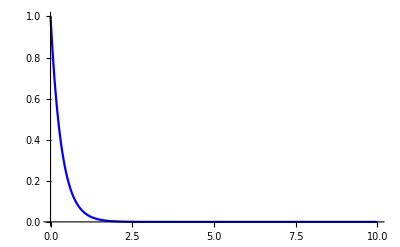

```mathematica
Plot[{ⅇ^(-3 t)},{t,0,10},PlotRange->All, PlotStyle->Blue]
```

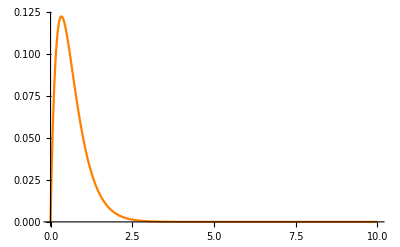

```mathematica
Plot[{ⅇ^(-3 t) t},{t,0,10},PlotRange->All, PlotStyle->Orange]
```

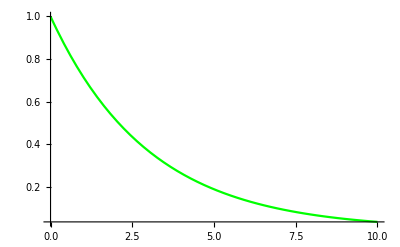

```mathematica
Plot[{ⅇ^(-t/3)},{t,0,10},PlotRange->All, PlotStyle->Green]
```

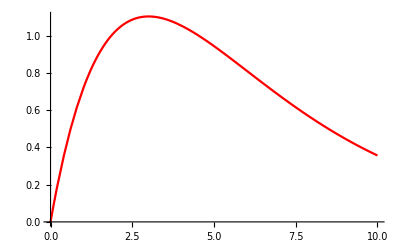

```mathematica
Plot[{ⅇ^(-t/3)t},{t,0,10},PlotRange->All, PlotStyle->Red]
```

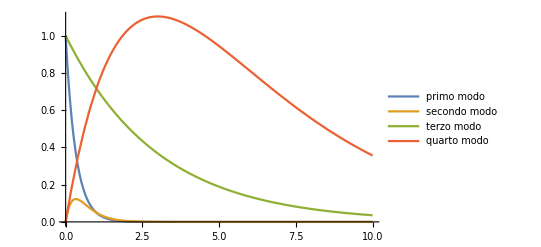

```mathematica
Plot[{{ⅇ^(-3 t)},{ⅇ^(-3 t)t},{ⅇ^(-t/3)},{ⅇ^(-t/3)t}},{t,0,10},PlotRange->All, PlotLegends->{"primo modo","secondo modo","terzo modo","quarto modo"}]
```

### Risposta libera del sistema

Carico lo stato iniziale x_o

```mathematica
Subscript[x, 0] = {{0},{1},{1},{-3}}
```

{{0},{1},{1},{-3}}

Calcolo z_0

```mathematica
Subscript[z, 0] = Inverse[T].Subscript[x, 0]
```

{{-325/128},{-175/32},{-59/128},{355/96}}

```mathematica
Subscript[z, 0]//MatrixForm
```

(-325/128
-175/32
-59/128
355/96)

Calcolo x_l

```mathematica
prova[t_] := Expand[T.MatrixExp[A t].Subscript[x, 0]]
```

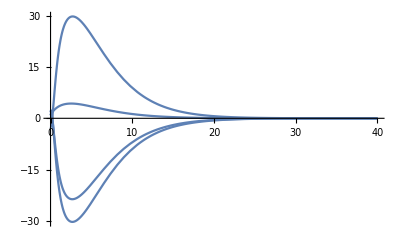

```mathematica
Plot[prova[t], {t,0,40}, PlotRange->All]
```

```mathematica
Subscript[x, l][t_] := Expand[T.MatrixExp[Λ t].Subscript[z, 0]]
```

```mathematica
Subscript[x, l][t]
```

{{-735/256 ⅇ^(-3 t)+(735 ⅇ^(-t/3))/256-1225/64 ⅇ^(-3 t) t+3479/576 ⅇ^(-t/3) t},{(49 ⅇ^(-3 t))/32-(17 ⅇ^(-t/3))/32+245/16 ⅇ^(-3 t) t-497/144 ⅇ^(-t/3) t},{(293 ⅇ^(-3 t))/128-(165 ⅇ^(-t/3))/128+595/32 ⅇ^(-3 t) t-781/288 ⅇ^(-t/3) t},{-325/128 ⅇ^(-3 t)-(59 ⅇ^(-t/3))/128-175/32 ⅇ^(-3 t) t+355/96 ⅇ^(-t/3) t}}

```mathematica
Subscript[x, l][t]//MatrixForm
```

(-735/256 ⅇ^(-3 t)+(735 ⅇ^(-t/3))/256-1225/64 ⅇ^(-3 t) t+3479/576 ⅇ^(-t/3) t
(49 ⅇ^(-3 t))/32-(17 ⅇ^(-t/3))/32+245/16 ⅇ^(-3 t) t-497/144 ⅇ^(-t/3) t
(293 ⅇ^(-3 t))/128-(165 ⅇ^(-t/3))/128+595/32 ⅇ^(-3 t) t-781/288 ⅇ^(-t/3) t
-325/128 ⅇ^(-3 t)-(59 ⅇ^(-t/3))/128-175/32 ⅇ^(-3 t) t+355/96 ⅇ^(-t/3) t)

Grafico

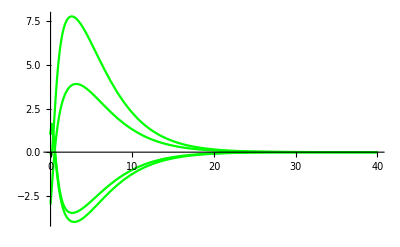

```mathematica
Plot[{Subscript[x, l][t]}, {t,0,40}, PlotRange->All, PlotStyle->Green]
```

Calcolo la risposta  libera nell’uscita

```mathematica
Subscript[y, l][t_] := Simplify[C1.Subscript[x, l][t]]
```

```mathematica
Subscript[y, l][t]
```

{{1/48 ⅇ^(-3 t) (ⅇ^(8 t/3) (885-7100 t)+9 (307+420 t))}}

```mathematica
{{1/48 ⅇ^(-3 t) (ⅇ^(8 t/3) (885-7100 t)+9 (307+420 t))}}
```

{{1/48 ⅇ^(-3 t) (ⅇ^(8 t/3) (885-7100 t)+9 (307+420 t))}}

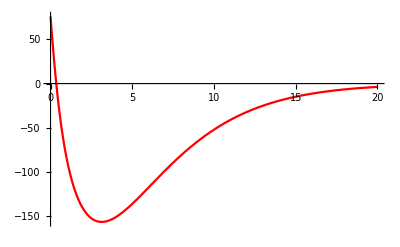

```mathematica
Plot[{Subscript[y, l][t]}, {t,0,20}, PlotRange->All, PlotStyle->Red]
```

### Configurazione stati che attivano i modi naturali

```mathematica
T//MatrixForm
```

(7/2 | -11/10 | 49/30 | 49/50
-14/5 | 51/50 | -14/15 | -13/50
-17/5 | 29/25 | -11/15 | -11/25
1 | 0 | 1 | 0)

Moltiplico la prima colonna per 1\3

```mathematica
Subscript[x, 1] = 1/3 T[[All,1]]
```

{7/6,-14/15,-17/15,1/3}

```mathematica
Subscript[x, l1c][t_] :=Expand[Simplify[MatrixExp[A t].Subscript[x, 1]]]
```

```mathematica
Subscript[x, l1c][t]
```

{(7 ⅇ^(-3 t))/6,-14/15 ⅇ^(-3 t),-17/15 ⅇ^(-3 t),ⅇ^(-3 t)/3}

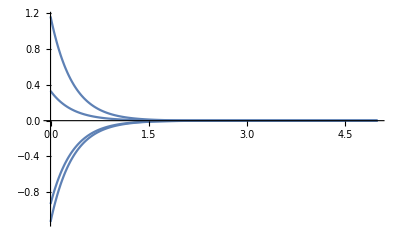

```mathematica
Plot[{Subscript[x, l1c][t]}, {t,0,5},PlotRange->All]
```

```mathematica
Subscript[x, 3] = 3T[[All,3]]
```

{49/10,-14/5,-11/5,3}

```mathematica
Subscript[x, l2c][t_] :=Expand[Simplify[MatrixExp[A t].Subscript[x, 3]]]
```

```mathematica
Subscript[x, l2c][t]
```

{(49 ⅇ^(-t/3))/10,-14/5 ⅇ^(-t/3),-11/5 ⅇ^(-t/3),3 ⅇ^(-t/3)}

```mathematica
Subscript[z, 222] := Simplify[Inverse[T].Subscript[x, 3]]
```

```mathematica
Subscript[x, l3c][t_]:=Expand[T.MatrixExp[Λ t].Subscript[z, 222]]
```

```mathematica
Subscript[x, l3c][t]
```

{(49 ⅇ^(-t/3))/10,-14/5 ⅇ^(-t/3),-11/5 ⅇ^(-t/3),3 ⅇ^(-t/3)}

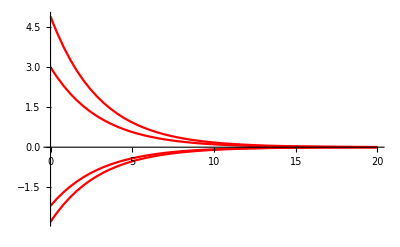

```mathematica
Plot[{Subscript[x, l2c][t]}, {t,0,20},PlotRange->All,PlotStyle->Red]
```

```mathematica
Subscript[z, 1]= Simplify[Inverse[T].Subscript[x, 1]]
```

{1/3,0,0,0}

```mathematica
Subscript[x, l1c2][t_] := Expand[T.MatrixExp[Λ t].Subscript[z, 1]]
```

```mathematica
Subscript[x, l1c2][t]
```

{(7 ⅇ^(-3 t))/6,-14/15 ⅇ^(-3 t),-17/15 ⅇ^(-3 t),ⅇ^(-3 t)/3}

```mathematica
Plot[{Subscript[x, l1c2][t]},{t,0,5}, PlotRange->All]
```

-Graphics-

### Funzione di trasferimento, poli e zeri

Calcolo la funzione di trasferimento dalla definizione

```mathematica
A = {{29/9, 49/3, -49/9, 49/9}, {-20/9, -43/3, 49/9, -49/9}, {-20/9, -46/3, 49/9, -58/9}, {2, 2, 1, -1}};
B = {{1}, {-1}, {-1}, {0}};
C1 = {{-8, 24, -32, -28}};
```

```mathematica
G[s_] := Simplify[C1.Inverse[s IdentityMatrix[4]-A].B]
```

```mathematica
G[s]
```

{{(36 (-3+s)^2)/((3+10 s+3 s^2)^2)}}

```mathematica
{{(36 (-3+s)^2)/((3+10 s+3 s^2)^2)}}
```

{{(36 (-3+s)^2)/((3+10 s+3 s^2)^2)}}

Trovo gli zeri di G[s]

```mathematica
Solve[Numerator[G[s][[1]]]== 0, s]
```

{{s→3},{s→3}}

Trovo i poli

```mathematica
Solve[Denominator[G[s][[1]]] == 0, s]
```

{{s→-3},{s→-3},{s→-1/3},{s→-1/3}}

Utilizzo un altro metodo con la funzione StateSpaceModel

```mathematica
Σ = StateSpaceModel[{A,B,C1}]
```

29/949/3-49/949/91-20/9-43/349/9-49/9-1-20/9-46/349/9-58/9-1221-10-824-32-280StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3$CellContext`stname4Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1141FalseFalseFalseAutomaticNoneAutomatic

Trovo la funzione di transizione G(s)

```mathematica
G1[s] = TransferFunctionModel[Σ]
```

(36-24 s+4 s^2)/(1+(20 s)/3+(118 s^2)/9+(20 s^3)/3+s^4)TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#s113611FalseFalseFalseAutomaticNoneAutomatic

Cerco i poli e gli zeri

```mathematica
TransferFunctionPoles[Σ]
```

{{{-3,-3,-1/3,-1/3}}}

```mathematica
TransferFunctionZeros[Σ]
```

{{{3,3}}}

I risultati sono esattamente gli stessi

### Risposta al gradino unitario e grafico

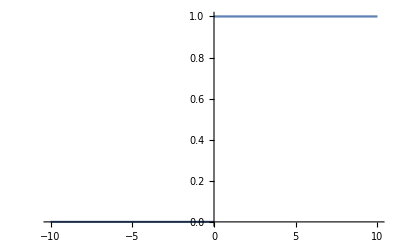

```mathematica
Plot[{UnitStep[t]},{t,-10,10},PlotRange->All]
```

Calcolo la risposta a gradino unitario come

```mathematica
Factor[G[s]LaplaceTransform[UnitStep[t],t,s]]
```

{{(36 (-3+s)^2)/(s (3+s)^2 (1+3 s)^2)}}

Ci sono poli multipli -3 2,

```mathematica
Y2[s]=Apart[G[s]/s]
```

{{36/s-27/(4 (3+s)^2)-81/(16 (3+s))-675/(4 (1+3 s)^2)-1485/(16 (1+3 s))}}

```mathematica
Subscript[Y, f][s_] := G[s](1/s)
```

```mathematica
Subscript[Y, f][s]
```

{{(36 (-3+s)^2)/(s (3+10 s+3 s^2)^2)}}

```mathematica
Subscript[D, 1](1/s)+Subscript[D, 11](1/(s+3))+Subscript[D, 12](1/(s+3)^2)+Subscript[D, 21](1/(s+1/3))+Subscript[D, 22](1/(s+1/3)^2)
```

D_1/s+D_11/(3+s)+D_12/(3+s)^2+D_21/(1/3+s)+D_22/(1/3+s)^2

```mathematica
Subscript[D, 1]= G[0]
```

{{36}}

```mathematica
Subscript[D, 12]= Limit[(s+3)^2 Subscript[Y, f][s],s->-3]
```

{{-27/4}}

```mathematica
der = D[(s+3)^2 Subscript[Y, f][s],s]
```

{{-(72 (-3+s)^2 (3+s)^2 (10+6 s))/(s (3+10 s+3 s^2)^3)+(72 (-3+s)^2 (3+s))/(s (3+10 s+3 s^2)^2)-(36 (-3+s)^2 (3+s)^2)/(s^2 (3+10 s+3 s^2)^2)+(72 (-3+s) (3+s)^2)/(s (3+10 s+3 s^2)^2)}}

```mathematica
Subscript[D, 11] =  Limit[der, s->-3]
```

{{-81/16}}

```mathematica
Subscript[D, 22]= Limit[(s+(1/3))^2 Subscript[Y, f][s],s->-(1/3)]
```

{{-75/4}}

```mathematica
der2 = D[(s+(1/3))^2 Subscript[Y, f][s],s]
```

{{-(72 (-3+s)^2 (1/3+s)^2 (10+6 s))/(s (3+10 s+3 s^2)^3)+(72 (-3+s)^2 (1/3+s))/(s (3+10 s+3 s^2)^2)-(36 (-3+s)^2 (1/3+s)^2)/(s^2 (3+10 s+3 s^2)^2)+(72 (-3+s) (1/3+s)^2)/(s (3+10 s+3 s^2)^2)}}

```mathematica
Subscript[D, 21]= Limit[der2, s->-(1/3)]
```

{{-495/16}}

```mathematica
InverseLaplaceTransform[Subscript[Y, f][s],s,t]
```

{{3/16 ⅇ^(-3 t) (-27-165 ⅇ^(8 t/3)+192 ⅇ^(3 t)-36 t-100 ⅇ^(8 t/3) t)}}

```mathematica
Subscript[y, f][t_]:=Subscript[D, 1] UnitStep[t]+Subscript[D, 11] Exp[-3 t]UnitStep[t]+Subscript[D, 12] t Exp[-3t]UnitStep[t]+Subscript[D, 21] Exp[-(1/3)t]UnitStep[t]+Subscript[D, 22] t Exp[-(1/3)t]
```

```mathematica
Subscript[y, f][t]
```

{{-75/4 ⅇ^(-t/3) t+36 UnitStep[t]-81/16 ⅇ^(-3 t) UnitStep[t]-495/16 ⅇ^(-t/3) UnitStep[t]-27/4 ⅇ^(-3 t) t UnitStep[t]}}

```mathematica
Plot[{Subscript[y, f][t],36}, {t,0,20}, PlotRange->All,
PlotLabels->{"Risposta forzata","Risposta a regime"}]
```

-Graphics-

Altro modo

```mathematica
Expand[Simplify[ComplexExpand[InverseLaplaceTransform[Subscript[Y, f][s],s,t]]]]
```

{{36-(81 ⅇ^(-3 t))/16-495/(16 (ⅇ^t)^(1/3))-27/4 ⅇ^(-3 t) t-(75 t)/(4 (ⅇ^t)^(1/3))}}

```mathematica
Plot[{36-(81 ⅇ^(-3 t))/16-495/(16 (ⅇ^t)^(1/3))-27/4 ⅇ^(-3 t) t-
(75 t)/(4 (ⅇ^t)^(1/3)),36,-(81 ⅇ^(-3 t))/16-495/(16 (ⅇ^t)^(1/3))-27/4 ⅇ^(-3 t) t-(75 t)/(4 (ⅇ^t)^(1/3))}
,{t,0,20},PlotRange->All,PlotLabels->{"Risposta forzata",
"Risposta a regime","Risposta transitoria"}]
```

-Graphics-

### Risposta al segnale periodico elementare

Come prima cosa vado a scegliere A, ,

```mathematica
Subscript[A, m] = 1; ω = 1; ψ = 0;
```

```mathematica
G[s]
```

{{(36 (-3+s)^2)/((3+10 s+3 s^2)^2)}}

```mathematica
U[s_] := LaplaceTransform[Subscript[A, m] Sin[t] UnitStep[t],t,s]
```

```mathematica
U[s]
```

1/(1+s^2)

La risposta forzata è prodotto tra G[s]U[s]

```mathematica
Subscript[Y, for][s_] := G[s]U[s]
```

```mathematica
Subscript[Y, for][s]
```

{{(36 (-3+s)^2)/((1+s^2) (3+10 s+3 s^2)^2)}}

Con la funzione Apart verifico la divisione in fratti semplici fatta da Mathematica, e noto che mathematica non spacchetta l’ultimo fratto, dunque avremo 6 fratti semplici, due dei quali saranno complessi e coniugati

```mathematica
Apart[Subscript[Y, for][s]]
```

{{81/(40 (3+s)^2)+1647/(800 (3+s))+405/(8 (1+3 s)^2)-405/(32 (1+3 s))+(18 (-4+3 s))/(25 (1+s^2))}}

```mathematica
InverseLaplaceTransform[Subscript[Y, for][s], s, t]
```

{{9/800 ⅇ^(-3 t) (183-375 ⅇ^(8 t/3)+180 t+500 ⅇ^(8 t/3) t+192 ⅇ^(3 t) Cos[t]-256 ⅇ^(3 t) Sin[t])}}

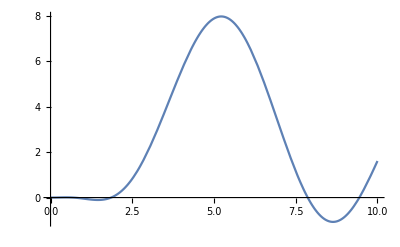

```mathematica
Plot[{9/800 ⅇ^(-3 t) (183-375 ⅇ^(8 t/3)+180 t+500 ⅇ^(8 t/3) t+192 ⅇ^(3 t) Cos[t]-256 ⅇ^(3 t) Sin[t])}, {t,0,10},PlotRange->All]
```

Scrivo ora i fratti semplici(scomponendo (1 + s^ 2)) e trovo i coefficienti

```mathematica
Subscript[F, 1]/(s - ⅈ)+Subscript[F, 2]/(s + ⅈ)+ Subscript[F, 11]/(s +3)+Subscript[F, 12]/(s + 3)^2+Subscript[F, 21]/(s +(1/3))+Subscript[F, 22]/(s + (1/3))^2
```

F_1/(-ⅈ+s)+F_2/(ⅈ+s)+F_11/(3+s)+F_12/(3+s)^2+F_21/(1/3+s)+F_22/(1/3+s)^2

Dobbiamo trovare F_1,F_2,... attraverso la formula di Heaviside non semplificata

```mathematica
Subscript[F, 1]= Limit[(s-ⅈ)Subscript[Y, for][s], s->ⅈ][[1,1]]
```

27/25+(36 ⅈ)/25

```mathematica
Subscript[F, 2]= Conjugate[Subscript[F, 1]]
```

27/25-(36 ⅈ)/25

```mathematica
Subscript[F, 22]= Limit[((1/3)+s)^2 Subscript[Y, for][s],s->-(1/3)][[1,1]]
```

45/8

```mathematica
der4= D[(1/3+s)^2 Subscript[Y, for][s],s]
```

{{-(72 (-3+s)^2 (1/3+s)^2 (10+6 s))/((1+s^2) (3+10 s+3 s^2)^3)-(72 (-3+s)^2 s (1/3+s)^2)/((1+s^2)^2 (3+10 s+3 s^2)^2)+(72 (-3+s)^2 (1/3+s))/((1+s^2) (3+10 s+3 s^2)^2)+(72 (-3+s) (1/3+s)^2)/((1+s^2) (3+10 s+3 s^2)^2)}}

```mathematica
Subscript[F, 21]= Limit[der4,s->-(1/3)][[1,1]]
```

-135/32

```mathematica
Subscript[F, 12]= Limit[(s + 3)^2 Subscript[Y, for][s], s->-3][[1,1]]
```

81/40

```mathematica
der5 = D[(3+s)^2 Subscript[Y, for][s],s]
```

{{-(72 (-3+s)^2 (3+s)^2 (10+6 s))/((1+s^2) (3+10 s+3 s^2)^3)-(72 (-3+s)^2 s (3+s)^2)/((1+s^2)^2 (3+10 s+3 s^2)^2)+(72 (-3+s)^2 (3+s))/((1+s^2) (3+10 s+3 s^2)^2)+(72 (-3+s) (3+s)^2)/((1+s^2) (3+10 s+3 s^2)^2)}}

```mathematica
Subscript[F, 11]= Limit[der5,s->-3][[1,1]]
```

1647/800

```mathematica
Subscript[F, 1]/(s - ⅈ)+Subscript[F, 2]/(s + ⅈ)+ Subscript[F, 11]/(s +3)+Subscript[F, 12]/(s + 3)^2+Subscript[F, 21]/(s +(1/3))+Subscript[F, 22]/(s + (1/3))^2
```

(27/25+(36 ⅈ)/25)/(-ⅈ+s)+(27/25-(36 ⅈ)/25)/(ⅈ+s)+45/(8 (1/3+s)^2)-135/(32 (1/3+s))+81/(40 (3+s)^2)+1647/(800 (3+s))

A questo punto vediamo la risposta a regime

```mathematica
Subscript[y, ss1][t_]:= 2ComplexExpand[Re[Subscript[F, 1] Exp[I t]]]
```

```mathematica
Subscript[y, ss1][t]
```

2 ((27 Cos[t])/25-(36 Sin[t])/25)

```mathematica
InverseLaplaceTransform[Subscript[Y, for][s],s,t][[1,1]]
```

9/800 ⅇ^(-3 t) (183-375 ⅇ^(8 t/3)+180 t+500 ⅇ^(8 t/3) t+192 ⅇ^(3 t) Cos[t]-256 ⅇ^(3 t) Sin[t])

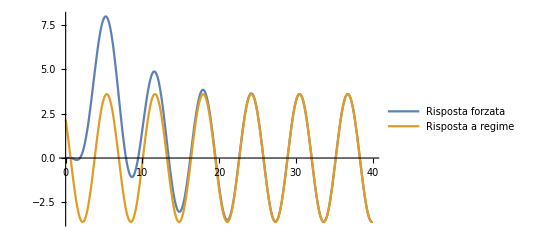

```mathematica
Plot[{9/800 ⅇ^(-3 t) (183-375 ⅇ^(8 t/3)+180 t+500 ⅇ^(8 t/3) t+192 ⅇ^(3 t) Cos[t]-256 ⅇ^(3 t) Sin[t]),
2 ((27 Cos[t])/25-(36 Sin[t])/25)},{t,0,40},PlotRange->All, 
PlotLegends->{"Risposta forzata", "Risposta a regime"}]
```

```mathematica
Solve[{(2 ((27 Cos[t])/25-(36 Sin[t])/25)== Amp Sin[t + θ])/. {t -> 0},
(D[2 ((27 Cos[t])/25-(36 Sin[t])/25),t]== D[Amp Sin[t + θ],t])/.{t->0},Amp>0},{Amp, θ}]
```

{{Amp→ConditionalExpression[18/5, C[1]∈ℤ],θ→ConditionalExpression[2 ArcTan[3]+2 π C[1], C[1]∈ℤ]}}

```mathematica
N[18/5]
```

3.6

```mathematica
N[2 ArcTan[3]](180/π)
```

143.13

```mathematica
nuovo = 3.6 Sin[t +2 ArcTan[3]]
```

3.6 Sin[t+2 ArcTan[3]]

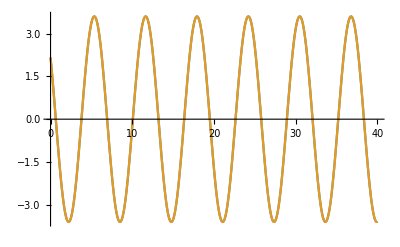

```mathematica
Plot[{nuovo, 2 ((27 Cos[t])/25-(36 Sin[t])/25)}, {t,0,40}, PlotRange->All]
```

### Modello ARMA equivalente e risposta a rampa unitaria

//File a parte

### Stato iniziale tale che risposta al gradino = risposta a regime

Incapsulo la terna A,B,C1

```mathematica
Σ  =StateSpaceModel[{A,B,C1}]
```

29/949/3-49/949/91-20/9-43/349/9-49/9-1-20/9-46/349/9-58/9-1221-10-824-32-280StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3$CellContext`stname4Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1141FalseFalseFalseAutomaticNoneAutomatic

Riprendo le cose che avevo calcolato in precedenza

```mathematica
G[s][[1,1]]
```

(36 (-3+s)^2)/((3+10 s+3 s^2)^2)

```mathematica
Eigenvalues[A]
```

{-3,-3,-1/3,-1/3}

```mathematica
JordanDecomposition[A][[2]]//MatrixForm
```

(-3 | 1 | 0 | 0
0 | -3 | 0 | 0
0 | 0 | -1/3 | 1
0 | 0 | 0 | -1/3)

```mathematica
Simplify[MatrixExp[Λ t]]//MatrixForm
```

(ⅇ^(-3 t) | ⅇ^(-3 t) t | 0 | 0
0 | ⅇ^(-3 t) | 0 | 0
0 | 0 | ⅇ^(-t/3) | ⅇ^(-t/3) t
0 | 0 | 0 | ⅇ^(-t/3))

Quelli che ritroviamo sono i modi del sistema , ora scriviamo il vettore dello stato iniziale

```mathematica
x0= {{x1},{x2},{x3},{x4}}
```

{{x1},{x2},{x3},{x4}}

```mathematica
lib = Simplify[C1.Inverse[s IdentityMatrix[4] - A].x0][[1,1]]
```

-(12 ((396+350 s+88 s^2+6 s^3) x1-2 (-189+47 s+45 s^2+9 s^3) x2+45 x3+426 s x3+181 s^2 x3+24 s^3 x3-171 x4-17 s x4+95 s^2 x4+21 s^3 x4))/((3+10 s+3 s^2)^2)

```mathematica
forz = Simplify[G[s](1/s)][[1,1]]
```

(36 (-3+s)^2)/(s (3+10 s+3 s^2)^2)

```mathematica
regim = (G[0](1/s))[[1,1]]
```

36/s

```mathematica
transitoria = Factor[forz - regim]
```

-(108 (1+s) (2+s) (11+3 s))/((3+s)^2 (1+3 s)^2)

```mathematica
Numerator[Simplify[Expand[lib + transitoria]]]
```

-12 (9 (22+44 x1+42 x2+5 x3-19 x4)+s (351+350 x1-94 x2+426 x3-17 x4)+3 s^3 (9+2 x1-6 x2+8 x3+7 x4)+s^2 (180+88 x1-90 x2+181 x3+95 x4))

```mathematica
CoefficientList[Numerator[Simplify[Expand[lib + transitoria]]],s]
```

{-108 (22+44 x1+42 x2+5 x3-19 x4),-12 (351+350 x1-94 x2+426 x3-17 x4),-12 (180+88 x1-90 x2+181 x3+95 x4),-36 (9+2 x1-6 x2+8 x3+7 x4)}

```mathematica
Solve[CoefficientList[Numerator[Simplify[Expand[lib + transitoria]]],s] == {0,0,0,0},{x1,x2,x3,x4}]
```

{{x1→-2,x2→1,x3→1,x4→-1}}

```mathematica
regim
```

36/s

```mathematica
OutputResponse[{Σ,{-2,1,1,-1}},1,t]
```

{36}

### Risposta al segnale u(t) = 1(-t)

Facciamo il grafico del segnale u(t) = 1(-t)

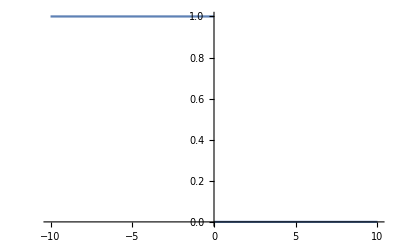

```mathematica
Plot[{UnitStep[-t]},{t,-10,10},PlotRange->All]
```

Ho applicato l’ingresso nel passato remoto, talmente remoto da non riuscire a vederlo
Ha senso calcolare questo risultato se il sistema è BIBO STABILE, difatti in t il transitorio si sarà esaurito

#### Valutazione della risposta per t < 0 (regime)

```mathematica
G[s_] := Simplify[(C1.Inverse[s IdentityMatrix[4] - A].B)[[1,1]]]
```

```mathematica
G[s]
```

(36 (-3+s)^2)/((3+10 s+3 s^2)^2)

```mathematica
Subscript[y, neg] = G[0]
```

36

#### Valutazione per t > 0, assenza di ingresso, ma a partire dalle condizioni iniziali legate alla commutazione da 1 a 0

Ricavo lo stato iniziale O x0 = condizioni iniziali
La matrice  che vado a costruire si chiama matrice di osservabilità che è invertibile se modi e poli coincidono, prima costruisco Ob poi mi assicuro che sia invertibile

```mathematica
Ob = {C1[[1]], (C1.A)[[1]], (C1.A.A)[[1]], (C1.A.A.A)[[1]]}
```

{{-8,24,-32,-28},{-64,-40,-28,60},{584/9,232/3,344/9,-92/9},{-1840/27,-5896/9,7172/27,-8204/27}}

Calcolo il determinante

```mathematica
Det[Ob]
```

-40960000

Calcolo ora lo stato iniziale utilizzando l’inversa della matrice di osservabilità(che esiste perchè il determinante è diverso da 0)

```mathematica
Subscript[x, 02] = Inverse[Ob].{{G[0]},{0},{0},{0}}
```

{{-3947/2000},{2089/2000},{983/1000},{-19/20}}

```mathematica
Subscript[y, liberas]= Simplify[(C1.Inverse[s IdentityMatrix[4]- A].Subscript[x, 02])[[1,1]]]
```

(36 (60+118 s+60 s^2+9 s^3))/((3+10 s+3 s^2)^2)

```mathematica
Apart[Subscript[y, liberas]]
```

27/(16 (3+s)^2)+117/(64 (3+s))+2187/(16 (1+3 s)^2)+6561/(64 (1+3 s))

Calcolo i fratti

```mathematica
Subscript[P, 12] = Limit[(s + 3)^2 Subscript[y, liberas],s-> -3]
```

27/16

```mathematica
Subscript[P, 11] = Limit[D[(s + 3)^2 Subscript[y, liberas], s],s-> -3]
```

117/64

```mathematica
Subscript[P, 22] = Limit[(s +(1/3))^2  Subscript[y, liberas],s-> -(1/3)]
```

243/16

```mathematica
Subscript[P, 21] = Limit[D[(s + (1/3))^2 Subscript[y, liberas],s], s ->-(1/3)]
```

2187/64

```mathematica
Subscript[y, liberat]= InverseLaplaceTransform[Subscript[y, liberas],s,t]
```

9/64 ⅇ^(-3 t) (13+12 t+27 ⅇ^(8 t/3) (9+4 t))

```mathematica
y[t_] :=Piecewise[{{Subscript[y, neg], t<0}, {Subscript[y, liberat], t>=0}}]
```

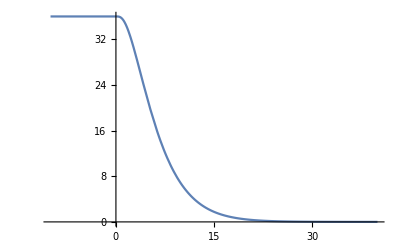

```mathematica
Plot[y[t], {t,-10,40}, PlotRange->All]
```